```mathematica
(*ClearAll["Global`*"]*)
path = "/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS/metcompc/Trabalho2/COP/COP/";
data = Table[Import[path <> ToString[StringForm["cop``.txt", beta/10.]],{"Table"}],{beta,1,9,1}];
```

```mathematica
(*lsquared=50*50;
iterationsReported = 500;
m=Manipulate[
ListPlot[
Select[Take[data[[beta*10]],{i*lsquared+1,(i+1)*lsquared}],#[[3]]==1&][[All,{1,2}]],PlotRange->{0,50},PlotStyle->{Red,PointSize[0.01]} ,Axes->False,AspectRatio->1],
{i,0,iterationsReported,1,AnimationRate->50},{beta,0.1,0.9,0.1}]*)
```

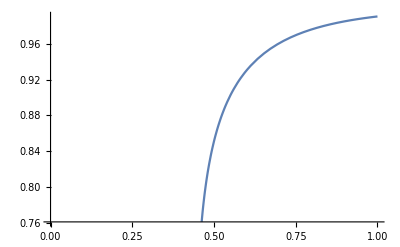

{0.0743315,0.925668,0.851337}

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{beta→-0.441379},{beta→0.441379}}

```mathematica
mf[beta_] := (1-Csch[2*beta*1]^2)^(1/8);
Plot[mf[beta],{beta,0,1}]
{(1-mf[0.5])/2,(1+mf[0.5])/2,mf[0.5]}
Solve[(1-Csch[2*beta*1]^2)^(1/8)==0.5,beta]
```

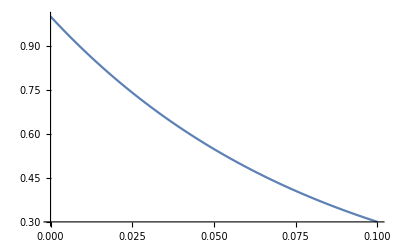

```mathematica
Plot[Exp[-beta*12],{beta,0,0.1}]
```

```mathematica
(*Table[path <> ToString[StringForm["cop``.txt", b]],{b,0.1,0.9,0.1}]*)
```

```mathematica
(*lsquared=50*50;
iterationsReported = 500;
m2[beta_]:=Manipulate[
ListPlot[
Select[Take[data[[beta*10]],{i*lsquared+1,(i+1)*lsquared}],#[[3]]==1&][[All,{1,2}]],PlotRange->{0,50},PlotStyle->{Red,PointSize[0.01]} ,Axes->False,AspectRatio->1],
{i,0,iterationsReported,1,AnimationRate->50}]
path ="/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS/metcompc/Trabalho2/COP/";
m2frames=Flatten@Table[m2[m1],{n1,0,iterationsReported,1},{m1,0.1,0.9,0.1}];
Export[path<> ToString[StringForm["COP_at_``.gif", 0.6]],frames]
(*Export[path<> ToString[StringForm["COP_at_``.gif", #]],m2[#]]&/@Range[0.1,0.9,0.1]*)*)
```

/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS/metcompc/Trabalho2/COP/COP_at_0.6.gif

```mathematica
(*frames=Flatten@Table[Manipulate[ContourPlot[q1/Norm[{x,y}-p[[1]]]+q2/Norm[{x,y}-p[[2]]],{x,-2,2},{y,-2,2},Contours->20,PlotRangePadding->0,Frame->False,PlotPoints->40,ImageSize->230,ColorFunction->"DarkRainbow"],{{q1,n1},-3,3},{{q2,m1},-3,3},{{p,{{-1,0},{1,0}}},{-1,-1},{1,1},Locator},Deployed->True,FrameMargins->0],{n1,-3,3},{m1,-3,3}];
Export["~/Desktop/frames.gif",frames];*)
```

```mathematica
(*Export[path<> ToString[StringForm["COP_at_``.avi", 0.1]],m2[0.1]]*)
```

```mathematica
lsquared=50*50;
iterationsReported = 100;
myFrames=Flatten@
Table[Manipulate[
ListPlot[
Select[Take[data[[beta*10]],{i*lsquared+1,(i+1)*lsquared}],#[[3]]==1&][[All,{1,2}]],PlotRange->{0,50},PlotStyle->{Red,PointSize[0.01]} ,Axes->False,AspectRatio->1],
{{i,n1},0,iterationsReported,1},{{beta,m1},0.1,0.9,0.1},Deployed->True,FrameMargins->0],{m1,0.1,0.9,0.1},{n1,0,iterationsReported,1}];
path ="/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS/metcompc/Trabalho2/COP/";
Export[path<>"cop.gif",myFrames];

(*Export[path<> ToString[StringForm["COP_at_``.gif", #]],m2[#]]&/@Range[0.1,0.9,0.1]*)
```

```mathematica
(*lsquared=50*50;
iterationsReported = 10;
myFrames=Flatten@
Table[Manipulate[
ListPlot[
Select[Take[data[[0.5*10]],{i*lsquared+1,(i+1)*lsquared}],#[[3]]==1&][[All,{1,2}]],PlotRange->{0,50},PlotStyle->{Red,PointSize[0.01]} ,Axes->False,AspectRatio->1],
{{i,n1},0,iterationsReported,1},Deployed->True,FrameMargins->0],{n1,0,iterationsReported,1}];
path ="/Users/diogofriggo/Google Drive/UFRGS 8o Semestre/METODOS/metcompc/Trabalho2/COP/";
Export[path<>"cop1.gif",myFrames];*)
```

```mathematica
(*Manipulate[
ListPlot[
Select[Take[data[[0.5*10]],{i*lsquared+1,(i+1)*lsquared}],#[[3]]==1&][[All,{1,2}]],PlotRange->{0,50},PlotStyle->{Red,PointSize[0.01]} ,Axes->False,AspectRatio->1],
{i,0,iterationsReported,1}]*)
```

Take::seqs: Sequence specification (+n, -n, {+n}, {-n}, {m, n}, or {m, n, s}) expected at position 2 in Take[{{0,0,1},{0,1,1},{0,2,1},{0,3,1},{0,4,1},{0,5,1},{0,6,1},{0,7,1},{0,8,1},{0,9,1},{0,10,1},{0,11,1},{0,12,1},{0,13,1},{0,14,1},{0,15,1},{0,16,1},{0,17,1},{0,18,1},{0,19,1},{0,20,1},«9»,{0,30,-1},{0,31,-1},{0,32,-1},{0,33,-1},{0,34,-1},{0,35,-1},{0,36,-1},{0,37,-1},{0,38,-1},{0,39,-1},{0,40,-1},{0,41,-1},{0,42,-1},{0,43,-1},{0,44,-1},{0,45,-1},{0,46,-1},{0,47,-1},{0,48,-1},{0,49,-1},«27450»},{«1»}].

Part::partw: Part 3 of {1+92 lsquared,93 lsquared} does not exist.

Take::argm: Take called with 0 arguments; 1 or more arguments are expected.

ListPlot::lpn: Take[] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

Take::take: Cannot take positions 230001 through 232500 in {{0,0,1},{0,1,1},{0,2,1},{0,3,1},{0,4,1},{0,5,1},{0,6,1},{0,7,1},{0,8,1},{0,9,1},{0,10,1},{0,11,1},{0,12,1},{0,13,1},{0,14,1},{0,15,1},{0,16,1},{0,17,1},{0,18,1},{0,19,1},{0,20,1},{0,21,1},«8»,{0,30,-1},{0,31,-1},{0,32,-1},{0,33,-1},{0,34,-1},{0,35,-1},{0,36,-1},{0,37,-1},{0,38,-1},{0,39,-1},{0,40,-1},{0,41,-1},{0,42,-1},{0,43,-1},{0,44,-1},{0,45,-1},{0,46,-1},{0,47,-1},{0,48,-1},{0,49,-1},«27450»}.

Part::partw: Part 3 of {230001,232500} does not exist.

Take::argm: Take called with 0 arguments; 1 or more arguments are expected.

ListPlot::lpn: Take[] is not a list of numbers or pairs of numbers.

General::stop: Further output of ListPlot::lpn will be suppressed during this calculation.

```mathematica
data
```

{{{0,0,1},{0,1,1},{0,2,1},{0,3,1},{0,4,1},{0,5,1},{0,6,1},{0,7,1},{0,8,1},{0,9,1},{0,10,1},{0,11,1},{0,12,1},{0,13,1},{0,14,1},{0,15,1},{0,16,1},{0,17,1},{0,18,1},1252463,{49,32,-1},{49,33,-1},{49,34,-1},{49,35,-1},{49,36,-1},{49,37,-1},{49,38,-1},{49,39,-1},{49,40,-1},{49,41,-1},{49,42,-1},{49,43,-1},{49,44,-1},{49,45,-1},{49,46,-1},{49,47,-1},{49,48,-1},{49,49,-1}},{1}}
 |  |  |  |

```mathematica
data[[1]]
```

{{0,0,1},{0,1,1},{0,2,1},{0,3,1},{0,4,1},{0,5,1},{0,6,1},{0,7,1},{0,8,1},{0,9,1},{0,10,1},{0,11,1},{0,12,1},{0,13,1},{0,14,1},{0,15,1},{0,16,1},{0,17,1},{0,18,1},{0,19,1},1252460,{49,30,1},{49,31,1},{49,32,1},{49,33,1},{49,34,1},{49,35,1},{49,36,1},{49,37,-1},{49,38,-1},{49,39,1},{49,40,-1},{49,41,-1},{49,42,1},{49,43,-1},{49,44,-1},{49,45,-1},{49,46,1},{49,47,-1},{49,48,1},{49,49,-1}}
 |  |  |  |